## Mini-Netzwerk

### Konstruktion

Dieses Arbeitsblatt dient zur Illustration der Rechnungen im Python-Code der Klasse Network

Konstruktor bekommt eine Liste zur Dimensionierung des Netzwerks, hier als Beispiel [3,3,2]

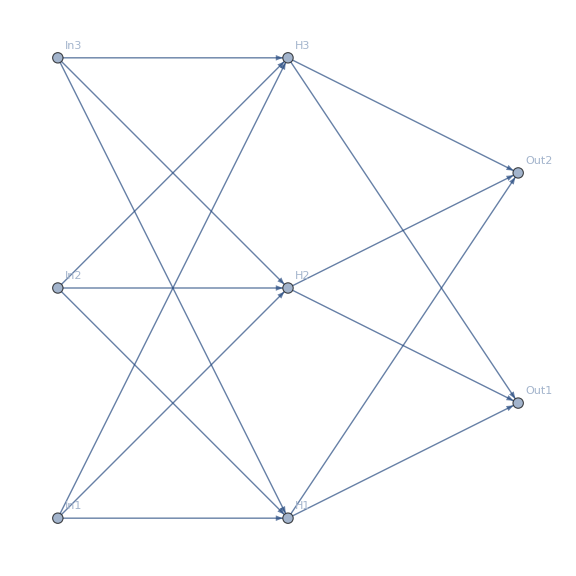
-Graphics- Null^6

```mathematica
sizes = {3,3,2};
```

Abgesehen von den Input-Neuronen der ersten Ebene bekommt jedes Neuron einen Bias-Parameter b

```mathematica
b = RandomReal[{0,1},#]&/@sizes[[2;;]];
MatrixForm[#ᵀ]&/@b
```

Part::take: Cannot take positions 2 through -1 in sizes.

RandomReal::array: The array dimensions sizes given in position 2 of RandomReal[{0,1},sizes] should be a list of non-negative machine-sized integers giving the dimensions for the result.

RandomReal::array: The array dimensions 2;;All given in position 2 of RandomReal[{0,1},2;;All] should be a list of non-negative machine-sized integers giving the dimensions for the result.

Part::pkspec1: The expression RandomReal[{0,1},2;;All] cannot be used as a part specification.

Part::pkspec1: The expression RandomReal cannot be used as a part specification.

Transpose[RandomReal[{0,1},sizes]]⟦Transpose[RandomReal[{0,1},2;;All]]⟧

```mathematica
w = RandomReal[{0,1},{#[[1]],#[[2]]}]&/@Transpose[{sizes[[;;2]],sizes[[2;;]]}];
MatrixForm[#ᵀ]&/@w
```

Part::take: Cannot take positions 1 through 2 in sizes.

Part::take: Cannot take positions 2 through -1 in sizes.

RandomReal::array: The array dimensions {sizes,1;;2} given in position 2 of RandomReal[{0,1},{sizes,1;;2}] should be a list of non-negative machine-sized integers giving the dimensions for the result.

RandomReal::array: The array dimensions {sizes,2;;All} given in position 2 of RandomReal[{0,1},{sizes,2;;All}] should be a list of non-negative machine-sized integers giving the dimensions for the result.

{Transpose[RandomReal[{0,1},{sizes,1;;2}]],Transpose[RandomReal[{0,1},{sizes,2;;All}]]}

```mathematica
sizes[[;;2]]
```

{3,3}

### FeedForward

Die Berechnung des Netzwerks für einen Aktivierungsvektor a_in, z.B. a_in=(0.4, 0.6, 1), ist jetzt nur lineare Algebra. Von Ebene a_i zu Ebene a_(i+1) wird die folgende Rechnung durchgeführt:

(a⃗)_(i+1)==σ(w_i·(a⃗)_i+(b⃗)_i)

 Und σ ist die  sogenannte Sigmoid-Funktion, die die Aktivierung in das Intervall [0,1] abbildet

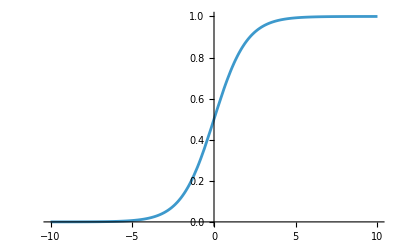

```mathematica
σ[x_]:=1/(1+ⅇ^-x)
Plot[σ[x],{x,-10,10}]
```

#### Beispiel

```mathematica
Subscript[a, in]={0.4,-0.6,1}
```

{0.4,-0.6,1}

```mathematica
Subscript[a, 2]=σ[w[[1]]ᵀ.Subscript[a, in]+b[[1]]ᵀ]
```

{0.510814,0.811037,0.775904}

```mathematica
Subscript[a, 3]=σ[w[[2]]ᵀ.Subscript[a, 2]+b[[2]]ᵀ]
```

{0.851434,0.866515}

### Stochastic Gradient Descent

#### backprop

Ziel ist es nun, die Gewichte und Biase so anzupassen, dass die Kostenfunktion minimal wird. Das ist ein typisches Minimierungsproblem. 
Dafür muss man bestimmen, wie die Kostenfunktion von den Parametern abhängt und die ersten Ableitungen (Gradienten) der Kostenfunktion bezüglich der Gewichte und Biase bestimmen. 

C==1/2((a⃗)_3-l⃗)^2==1/2(σ(w_2·(a⃗)_2+(b⃗)_2)-l⃗)^2==1/2(σ(w_2·σ(w_1·(a⃗)_1+(b⃗)_1)+(b⃗)_2)-l⃗)^2

Das ruft die Kettenregel auf den Plan. Die äußerste Ableitung ist lediglich der Gradient der Kostenfunktion.

#### cost_derivative

Einfachste Kostenfunktion: Quadrate der Differenzen zwischen Label und Aktivierung, z.B.

```mathematica
Cost[a_,l_]:=1/2(a-l).(a-l)
```

```mathematica
Cost[Subscript[a, 3],{1,0}]
```

1/2 ((-1+a_3)^2+a_3^2)

Der Gradient der Kostenfunktion ist

```mathematica
DC[a_,l_]:=(a-l)
```

Dieser Gradient wird nahe des Minimums sehr klein und das Training dauert dann sehr lang. Effektivere Kostenfunktionen sind zum Beispiel die Cross-Entropie-Funktion

```mathematica
a*x^2+b*x+c
```